```mathematica
Needs["NeffConstraint`"]
```

### Analytic preliminaries

#### LIPS out of COM

```mathematica
Clear[M2]
dΠLIPS=dΩ/(16 π^2) kD/Ei /.Ei ->p + mD
dΠi = (nD g)/(mD p)     (dp  p^2)/(8 π^2)1/(E^(β p)+1)
Integrand = Simplify[Simplify[dΠLIPS dΠi M2 Et]]
```

(dΩ kD)/(16 (mD+p) π^2)

(dp g nD p)/(8 (1+ⅇ^(p β)) mD π^2)

(d^2 dp dΩ g kD M2 nD p^3)/(64 (1+ⅇ^(p β)) (mD+p) (-d^2 p^2+(mD+p)^2) π^4)

Mandelstam variables

```mathematica
s = Simplify[(mD + p)^2 - p^2]
t = Simplify[(Et)^2 - q^2]
u = FullSimplify[(Ef - mD)^2-Ef^2]
```

mD (mD+2 p)

-(4 d^2 mD^2 p^2)/(mD^2+2 mD p-(-1+d^2) p^2)

(mD (mD^3+3 (-1+d^2) mD p^2+2 (-1+d^2) p^3))/((mD+p-d p) (mD+p+d p))

```mathematica
Et
```

(2 d^2 mD p^2)/(-d^2 p^2+(mD+p)^2)

```mathematica
M2lD =FullSimplify[(8 e^2 eD^2 ϵ^2)/t^2((s/2)^2+(u/2)^2)] (*lepton dark matter scattering*)
```

1/(4 d^4 mD^2 p^4)e^2 eD^2 (mD^6+4 mD^5 p+2 (5+d^2) mD^4 p^2-4 (-5+d^2) mD^3 p^3+(25-22 d^2+5 d^4) mD^2 p^4+8 (2-3 d^2+d^4) mD p^5+4 (-1+d^2)^2 p^6) ϵ^2

```mathematica
Integrand/.M2->M2lD
```

(dp dΩ e^2 eD^2 g kD nD (mD^6+4 mD^5 p+2 (5+d^2) mD^4 p^2-4 (-5+d^2) mD^3 p^3+(25-22 d^2+5 d^4) mD^2 p^4+8 (2-3 d^2+d^4) mD p^5+4 (-1+d^2)^2 p^6) ϵ^2)/(256 d^2 (1+ⅇ^(p β)) mD^2 p (mD+p) (-d^2 p^2+(mD+p)^2) π^4)

```mathematica
Integrate[Integrand,d]
```

(dp dΩ g kD M2 nD (-2 d p-(mD+p) Log[-mD+(-1+d) p]+(mD+p) Log[mD+p+d p]))/(128 (1+ⅇ^(p β)) (mD+p) π^4)

```mathematica
Simplify[2 π/dΩ Integrate[Integrand/.M2->M2lD,d]]
FullSimplify[((%/.d->1)-(%/.d->-1))/mD^2]
```

(dp e^2 eD^2 g kD nD ϵ^2 (-((mD+p)^2 (mD^2+4 p^2))/d-d p^2 (5 mD^2+8 mD p+4 p^2)-4 mD^2 p (mD+p) Log[mD+p-d p]+4 mD^2 p (mD+p) Log[mD+p+d p]))/(128 (1+ⅇ^(p β)) mD^2 p (mD+p) π^3)

-((dp e^2 eD^2 g kD nD ϵ^2 (mD^4+2 mD^3 p+10 mD^2 p^2+16 mD p^3+8 p^4+4 mD^2 p (mD+p) (Log[mD]-Log[mD+2 p])))/(64 (1+ⅇ^(p β)) mD^4 p (mD+p) π^3))

#### Massive case - in momentum variables

compute q and compare to massless case

```mathematica
Clear[θsol,d]
θsol = Solve[mD + √(p^2+m^2) == √(mD^2 + kD^2) + √(p^2 - 2 p d kD + kD^2 + m^2),d][[1]]
d= Simplify[d/.θsol]
PowerExpand[Series[d,{kD,0,1}]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{d→(-mD^2+mD √(kD^2+mD^2)-mD √(m^2+p^2)+√(kD^2+mD^2) √(m^2+p^2))/(kD p)}

((-mD+√(kD^2+mD^2)) (mD+√(m^2+p^2)))/(kD p)

((mD+√(m^2+p^2)) kD)/(2 mD p)+O[kD]^2

```mathematica
Simplify[D[d,kD]/d]
```

mD/(kD √(kD^2+mD^2))

```mathematica
Simplify[D[d,kD]/d]
```

mD/(kD √(kD^2+mD^2))

Compute E transfered

```mathematica
(*Ef = FullSimplify[√(p^2 - 2 kD d p +kD^2+m^2)/.θsol]*)
Ef = FullSimplify[mD +√(p^2+m^2) - √(mD^2 + kD^2)]
Et =FullSimplify[√(mD^2 + kD^2)-mD]
ESM = √(p^2+m^2)
Ei = ESM + mD
```

mD-√(kD^2+mD^2)+√(m^2+p^2)

-mD+√(kD^2+mD^2)

√(m^2+p^2)

mD+√(m^2+p^2)

```mathematica
Simplify[Expand[(ESMt + mD)^2/(ESMt^2-m^2) -1]]
```

(m^2+2 ESMt mD+mD^2)/(ESMt^2-m^2)

```mathematica
s=Simplify[(mD + ESM)^2-p^2] (*p + pD squared*)
t = Simplify[ (Et)^2- kD^2](*kD - pD squared*)
(*u = Simplify[(Ef-mD)^2-√(Ef^2-m^2)](*k - pD squared*)*)
u = Simplify[(Ef-mD)^2-(Ef^2-m^2)](*k - pD squared*)
```

m^2+mD (mD+2 √(m^2+p^2))

2 mD (mD-√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[m^2-mD^2+2mD Ei](*s*)
Simplify[-2mD Et] (*t*)
Simplify[2(m^2+mD^2)-t-s] (*u*)
Simplify[m^2+mD^2-2mD Ef] (*u*)
Simplify[m^2+3mD^2+2mD (Et-Ei)] (*u*)
```

m^2+mD (mD+2 √(m^2+p^2))

-2 mD (-mD+√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[m^2+mD^2+2mD ESM](*s*)
Simplify[-2mD Et] (*t*)
Simplify[2(m^2+mD^2)-t-s] (*u*)
Simplify[m^2+mD^2-2mD Ef] (*u*)
Simplify[m^2+mD^2+2mD (Et-ESM)] (*u*)
```

m^2+mD (mD+2 √(m^2+p^2))

-2 mD (-mD+√(kD^2+mD^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

m^2+mD (-mD+2 √(kD^2+mD^2)-2 √(m^2+p^2))

```mathematica
Simplify[u+t+s]
```

2 (m^2+mD^2)

#### Millicharge Paper - DS populated after Recombination

```mathematica
Print["The rough temperature at which the dark photon bath can be populated is:"]
Tγ=10^7 GeV (gp/0.1)^2 ϵ/10^-8 
Print["Now solve for ϵ st the dark photon bath is populated at recombination"]
Solve[Tγ == TR,ϵ][[1]]
Print["Where TR is Recombination temperature gp is dark coupling. For gp=0.1 we have"]
%%/.{gp->0.1,TR ->0.25 10^-9 GeV}
```

The rough temperature at which the dark photon bath can be populated is:

1.×10^17 GeV gp^2 ϵ

Now solve for ϵ st the dark photon bath is populated at recombination

{ϵ→(1.×10^-17 TR)/(GeV gp^2)}

Where TR is Recombination temperature gp is dark coupling. For gp=0.1 we have

{ϵ→2.5×10^-25}

### Analyze Cosmology of aDM between recombination and annihilation - Neff

```mathematica
CosmoParams[]
```

{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}

#### Initialize

```mathematica
inter1me=InterpolateEtransRate[me,me,1];
inter2000me=InterpolateEtransRate[2000 me,me,1];
```

$Aborted

```mathematica
testΔEdict =InterpolateTotEtrans[{ ("me"/.CosmoParams[])10^-9,("me"/.CosmoParams[])10^4 },("me"/.CosmoParams[]),1,CosmoParams[]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 2.72523×10^16 and 8.434×10^13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 1.24981×10^16 and 1.72128×10^12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 2.18099×10^17 and 1.94891×10^15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
testΔEdictkis0 =InterpolateTotEtrans[{ ("me"/.CosmoParams[])10^-9,("me"/.CosmoParams[])10^4 },("me"/.CosmoParams[]),1,CosmoParams[]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 2.72523×10^16 and 8.434×10^13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 1.24981×10^16 and 1.72128×10^12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.000202728}. NIntegrate obtained 2.18099×10^17 and 1.94891×10^15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

#### Plot hubble and aH

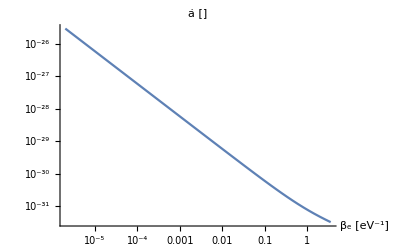

```mathematica
LogLogPlot[aH[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"ȧ []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

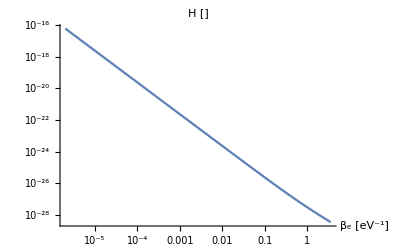

```mathematica
LogLogPlot[H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"H []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

#### Screening length comparison and Expected rate scaling

Λ and 1/(Z_1 β ȧ) control the scaling of the rate

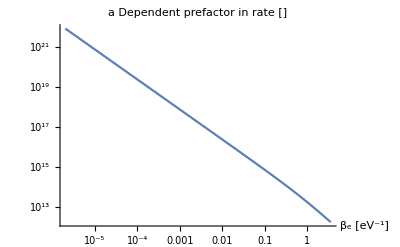

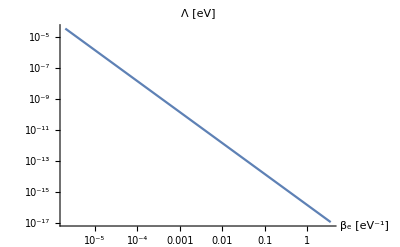

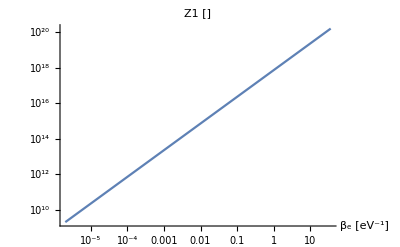

```mathematica
LogLogPlot[1/(Z1[β] aH[β]β)/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"a Dependent prefactor in rate []",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Λ[β,"me"]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Z1[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],10/("TR")/.CosmoParams[]},PlotLabel->"Z1 []",AxesLabel->{"β_e [eV^-1]"}]
```

So it seems like partition function dominates over temperature scaling of a, and the reduced screening at late times.

```mathematica
Z1[1/("Td")]/.CosmoParams[]
```

2.00913×10^9

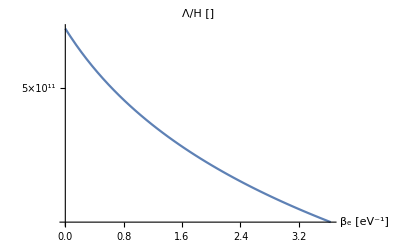

```mathematica
LogPlot[Λ[β,"me"]/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Screening length (Debeye momentum) - minimum momentum transfered

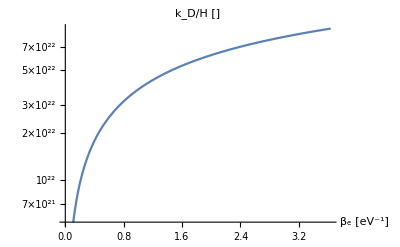

```mathematica
LogPlot[(√(2 "me" Λ[β,"me"]))/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

#### Rate and Energy plots - SM aDM mass values

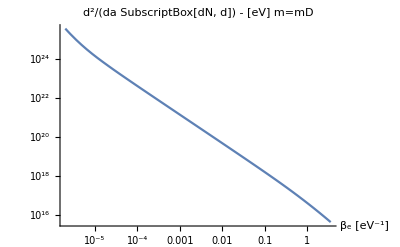

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

m=mD

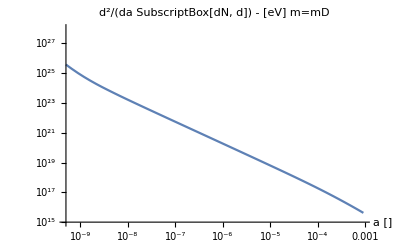

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

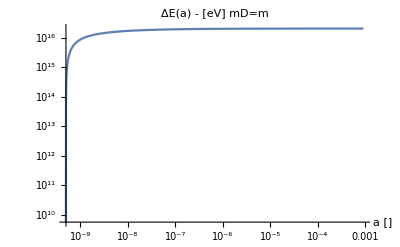

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->All]
```

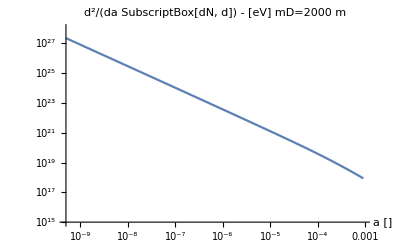

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

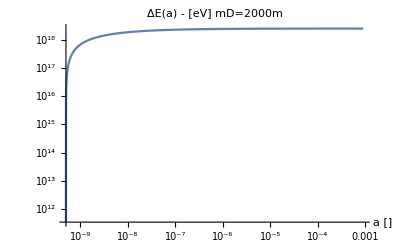

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->All]
```

#### Neff constraint

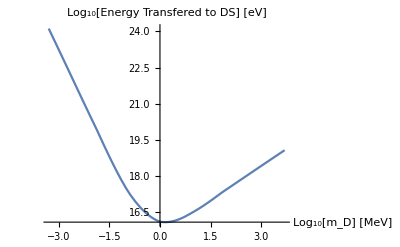

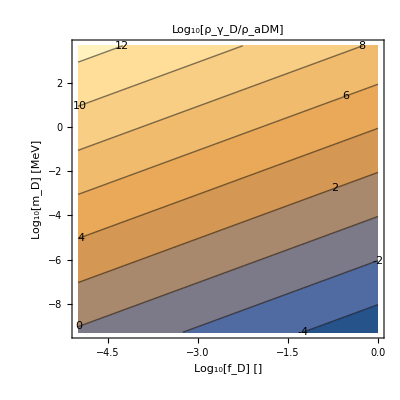

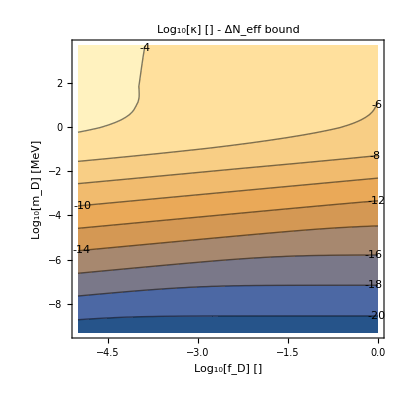

```mathematica
ComputeΔNeffConstraint[testΔEdict]
```

-Graphics-

-Graphics-

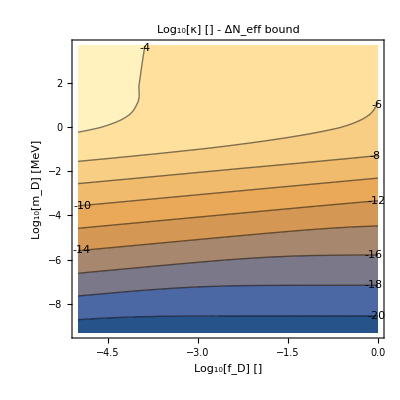

```mathematica
ComputeΔNeffConstraint[testΔEdict]
```

#### Interaction Rate - IR domination Debugging

```mathematica
(*ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ,params_]:=(m/.params)/ξβ NIntegrate[ NumIntegrand[mD,m,κ,ξβ,ξE,params],{ξE,0,∞}](*extra factor comes from jacobian*)*)
```

```mathematica
inter1me=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

```mathematica
interrate1me=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[],0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

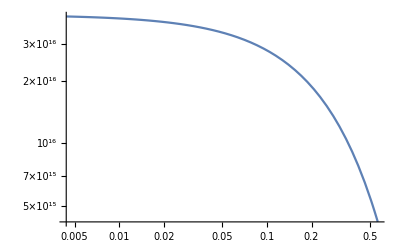

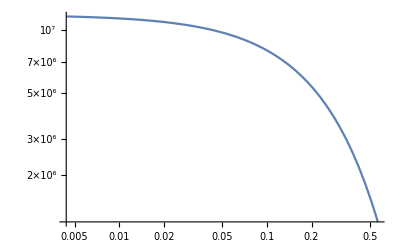

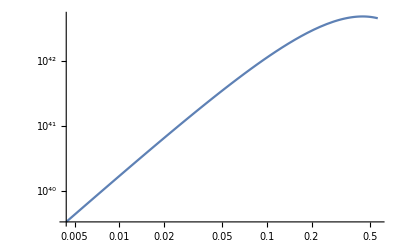

```mathematica
LogLogPlot[10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
LogLogPlot[nDR[10^-2,interrate1me[["mD"]]]10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
LogLogPlot[(10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]])/H[β]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
```

```mathematica
nDR[10^-2,10^6]/.CosmoParams[]
```

1.42034×10^-10

```mathematica
Plot[NeffConstraint`ESMIntegral["me"/.CosmoParams[],"me"/.CosmoParams[],1,ξβ,CosmoParams[],1],{ξβ,1,10^6}]
```

$Aborted

```mathematica
?ESMIntegral
```

```mathematica
NeffConstraint`NumIntegrand["me"/.CosmoParams[],"me"/.CosmoParams[],1,10^5,10^-5,CosmoParams[],0]
```

0.293113

```mathematica
Block[{l=1,Integrand,params=CosmoParams[],v1,v2,v3},
v1=Simplify[Integrate[Ett^l/(Ett+"Λ")^2 (("ms" + "ESMt")^2+("ms"+(Ett-"ESMt"))^2),Ett]];
	v2=Simplify[v1/."ms"->("m"^2+"mD"^2)/(2 "mD")];
	v3 =Simplify[Simplify[(v2/.Ett->(2 "mD")/(("ESMt"+"mD")^2/("ESMt"^2-"m"^2)-1))-(v2/.Ett->0)]];
Integrand=2/π ("α"^2 κ^2)/mDt (E^(-"β" "ESMt" + "β" "μ")/aH["β"]^l v3 /."μ"->"m" - 1/"β" Log["Qt"]/.{"Λ"->Λ["β","me"],"Qt"->Z1["β"]}/."ESMt"->1/"β" ξE + "m"/."β"->ξβ/"m"/.{"m"->mt,"mD"->mDt})/.params;
(*Print[v1];
Print[v2];*)
(*Print[Integrand];*)
Print[Integrand/.{"m"->"me"/.CosmoParams[],"mD"->"me"/.CosmoParams[],"κ"->1}/.CosmoParams[]]
]
```

(8.95453×10^31 ⅇ^(-((mt+(mt ξE)/ξβ) ξβ)/mt+(ξβ (mt-(mt Log[(7.10335×10^17)/(mt/ξβ)^(3/2)])/ξβ))/mt) mt κ^2 (-((mDt^2+mt^2)^2)/(2 mDt^2)+(2 (mt^2+mDt (mDt-2 (mt+(mt ξE)/ξβ)-(2.91415×10^-16 mt^2)/ξβ^2)) (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(2 mDt^2)/((-1+(mDt+mt+(mt ξE)/ξβ)^2/(-mt^2+(mt+(mt ξE)/ξβ)^2))^2)-2 (mt+(mt ξE)/ξβ)^2-(2.12306×10^-32 mt^4)/ξβ^4+(1.45707×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(1.45707×10^-16 mt^2 (((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(2.12306×10^-32 mt^4)/ξβ^4-(1.45707×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(2.91415×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2))/(((2 mDt (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(1.45707×10^-16 mt^2)/ξβ^2) ξβ^2)-(2.91415×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2+(((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(6.36919×10^-32 mt^4)/ξβ^4-(2.91415×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(5.82829×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2) Log[(2 mDt (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(1.45707×10^-16 mt^2)/ξβ^2]-(((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(6.36919×10^-32 mt^4)/ξβ^4-(2.91415×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(5.82829×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2) Log[(1.45707×10^-16 mt^2)/ξβ^2]))/(mDt √(0.68+(2.4064×10^10 mt^4)/ξβ^4+(2.048×10^10 mt^3)/ξβ^3+(160000. mt^2)/ξβ^2) ξβ)

```mathematica
-2 ("ESMt"-"ms"+"Λ") Ett+Ett^2/2+("Λ" (2 ("ESMt")^2+2 ("ms")^2+2 "ESMt" "Λ"-2 "ms" "Λ"+("Λ")^2))/("Λ"+Ett)+(2 ("ESMt")^2+2 ("ms")^2+4 "ESMt" "Λ"-4 "ms" "Λ"+3 ("Λ")^2) Log["Λ"+Ett]/."ms"->("m"^2+"mD"^2)/(2 "mD")
Simplify[%]
```

-2 (ESMt-(m^2+mD^2)/(2 mD)+Λ) Ett+Ett^2/2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/(Λ+Ett)+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ+Ett]

((m^2+mD (-2 ESMt+mD-2 Λ)) Ett)/mD+Ett^2/2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/(Λ+Ett)+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ+Ett]

```mathematica
-1/(DΣ-1)+Simplify[-1/(DΣ-1)+DΣ/(DΣ-1)^2]
Simplify[(1-DΣ/(DΣ-1))^2]
```

1/(-1+DΣ)^2-1/(-1+DΣ)

1/(-1+DΣ)^2

### CMB Distortion

#### Yushin’s BOTE Calculation from CMB distortion

Today

```mathematica
(α^2 ϵ^2 Mpl)/T0^4(eV^3 nD0[0.01,10^9]/.CosmoParams[] ) /.{α->1/137,T0->("T0"/.CosmoParams[]) eV,Mpl->10^28 eV}(*Γ/H using aDM fraction of order a percent*)
ϵ/.Solve[%==1,ϵ][[2]]
```

1.4555×10^16 ϵ^2

8.28884×10^-9

At Recombination

```mathematica
(α^2 ϵ^2 Mpl)/T^4(eV^3 nD0[0.01,10^5](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->("TR"/.CosmoParams[]) eV,Mpl->10^28 eV}(*Γ/H using aDM fraction of order a percent*)
ϵ/.Solve[%==1,ϵ][[2]]
```

1.32318×10^17 ϵ^2

2.7491×10^-9

```mathematica
(α^2 ϵ^2 Mpl)/T^4 r^-1(eV^3 nD0[0.01,10^9](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->("TR"/.CosmoParams[]) eV,Mpl->10^28 eV,r->10^-4}
PowerExpand[%]^-1 ϵ^2
```

1.32318×10^17 ϵ^2

7.55754×10^-18

```mathematica
(α^2 ϵ^2 Mpl)/(T^3 me) r^-1(eV^3 nD0[0.01,10^9](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->("TR"/.CosmoParams[]) eV,Mpl->10^28 eV,r->10^-4,me->"me"eV/.CosmoParams[]}
PowerExpand[%]^-1 ϵ^2
```

7.2775×10^10 ϵ^2

1.3741×10^-11

Yushin was also saying something about DOFs and entropy sharing

100 units of total energy stay in SM sector (some temperature, rad dominated), DS is in TE with SM so entropy split among DS and SM dofs => change of temperature, must be less than 10^{-5}. \Delta N_{eff} is from cosmo bounds etc.
Assumption here seems to be that the sectors equilibriate if they scatter at all.

```mathematica
(α^2 ϵ^2)/T^2(eV^3 nD0[0.01,10^5](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->("TR"/.CosmoParams[]) eV,Mpl->10^28 eV,r->10^-5}
```

1.00066×10^-12 eV ϵ^2

#### Squiggly CMB distortion using our interaction rate

get interaction rate (over n_D) for elecron mass aDM scattering off SM electrons with κ=(α_D ϵ)/α = 1

```mathematica
intratemDisme=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[],0];
```

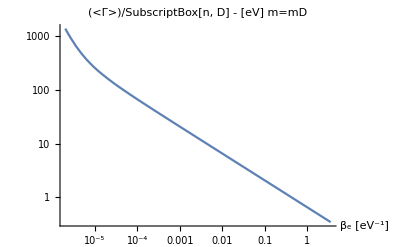

```mathematica
LogLogPlot[10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"(<Γ>)/SubscriptBox[n, D] - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

this shows the interaction rate scales as T^(1/2) near recombination

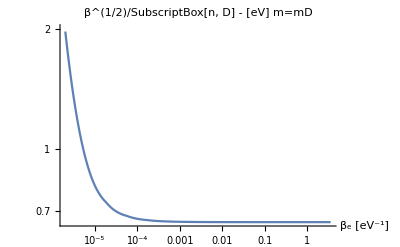

```mathematica
LogLogPlot[β^(1/2)10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"β^(1/2)/SubscriptBox[n, D] - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"},PlotRange->{0,2}]
```

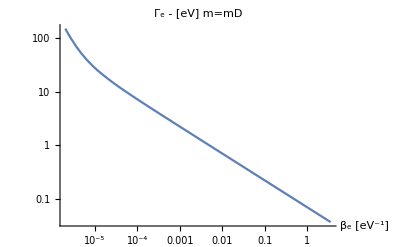

```mathematica
LogLogPlot[(nD0[0.01,1000"me"/.CosmoParams[]]/.CosmoParams[])/("n0"/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Γ_e - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

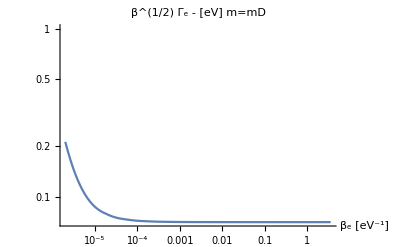

```mathematica
LogLogPlot[β^(1/2)(nD0[0.01,1000"me"/.CosmoParams[]]/.CosmoParams[])/("n0"/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"β^(1/2) Γ_e - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"},PlotRange->{0,1}]
```

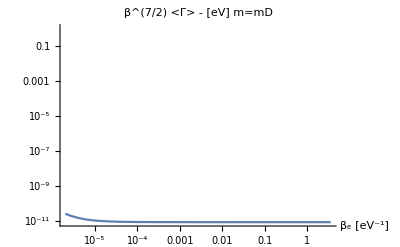

```mathematica
LogLogPlot[β^(7/2)(nD0[0.01,1000"me"/.CosmoParams[]](1/(β "T0"))^3/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"β^(7/2) <Γ> - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"},PlotRange->{0,1}]
```

Now compute ((Γ̄)_e)/H

```mathematica
(*H=1/(10^28 eV β^2)*)
ΓebarbyH=1/(H[β]/.CosmoParams[])((nD0[0.01,1000"me"/.CosmoParams[]]/.CosmoParams[])/("n0"/.CosmoParams[]))10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]]/.β->(1/("TR")/.CosmoParams[])
```

1.03254×10^27

```mathematica
ϵ^2== r/ΓebarbyH/.r->10^-5
```

ϵ^2==9.68485×10^-33

This is much too stringent. Now compute (n_e(Γ̄)_e)/H

```mathematica
(*H=1/(10^28 eV β^2)*)
ΓebarbyH=1/(H[β]/.CosmoParams[])(nD0[0.01,1000"me"/.CosmoParams[]](1/(β "T0"))^3/.CosmoParams[])10^intratemDisme[["f"]][Log10[β "me"/.CosmoParams[]]]/.β->(1/("TR")/.CosmoParams[])
```

2.71448×10^15

```mathematica
ϵmax = √(r/ΓebarbyH)/.r->10^-4
```

1.91936×10^-10

```mathematica
"n0"(("TR")/("T0"))^3/.CosmoParams[]
```

2.62894×10^-12

```mathematica
("TR")^-3/.CosmoParams[]
```

48.0841

#### Full Calculation

```mathematica
(*Clear[InterPoints,integrand,Interξβs,TB,TR,T0]*)
```

```mathematica
(*testInterpolatey[mD_,m_,mpD_,fD_,κ_,params_,l_:1]:=Module[{n=13,Interξβs,InterPoints,yLogFnofβ,yprefactor,y,TB,TR,T0},

TB = "TB"/.params; (*brehmstrahlung inefficiency*)
TR = "TR" /.params; (*recombination*)
T0 = "T0"/.params; (*today*)

(*Interpolate to find the energy transfer rate between e e decoupling and recombination*)
Interξβs= Subdivide[Log10[m/TB],Log10[m/TR],n]; (*points to be samples, we have made β dimensionless (ξβ=m β)*)
Print[Interξβs];
yprefactor= T0/4(nD0[fD,mpD]/(T0^3 β^3))(π^2/30 2)^-1 β^4/.params;
Print[Table[(yprefactor /.β->10^Interξβs[[i]]/m),{i,Length[Interξβs]}]];
InterPoints=Table[{Interξβs[[i]],Log10[Abs[(yprefactor /.β->10^Interξβs[[i]]/m)ESMIntegral[mD,m,κ,10^Interξβs[[i]],params,l]]]},{i,Length[Interξβs]}] ;
Print[InterPoints];(*Abs since numerical instability at early times*)
(*computed in the notes*)
yLogFnofβ=Interpolation[InterPoints];
y = NIntegrate[10^yLogFnofβ[Log10[β m]],{β,1/TB,1/TR}];
(*RateFnofβ[β_] := 10^RateLogFnofβ[Log10[β m]];*)
(*<|"f"->RateFnofβ,"LogLogf"->RateLogFnofβ,"ξβ"->Interξβs,"Points"->InterPoints|>*)
<|"f"->yLogFnofβ,"y"->y,"ξβ"->Interξβs,"Points"->InterPoints,"mD"->mD,"m"->m,"κ"->κ,"params"->params|>
]*)
```

```mathematica
(*Interpolatey["me"/.CosmoParams[],"me"/.CosmoParams[],2000"me"/.CosmoParams[],0.01,1,CosmoParams[]]*)
```

{{2.30103,3.15653},{2.60554,3.01417},{2.91005,2.87203},{3.21455,2.72976},{3.51906,2.58707},{3.82357,2.4436},{4.12808,2.2987},{4.43259,2.15118},{4.7371,1.99883},{5.0416,1.8378},{5.34611,1.66229},{5.65062,1.46552},{5.95513,1.24287},{6.25964,0.99499}}

<|f→InterpolatingFunction[…],y→101.774,ξβ→{2.30103,2.60554,2.91005,3.21455,3.51906,3.82357,4.12808,4.43259,4.7371,5.0416,5.34611,5.65062,5.95513,6.25964},Points→{{2.30103,3.15653},{2.60554,3.01417},{2.91005,2.87203},{3.21455,2.72976},{3.51906,2.58707},{3.82357,2.4436},{4.12808,2.2987},{4.43259,2.15118},{4.7371,1.99883},{5.0416,1.8378},{5.34611,1.66229},{5.65062,1.46552},{5.95513,1.24287},{6.25964,0.99499}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,aB→1/10000000,TB→2500.,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

```mathematica
CMBdisty=Interpolatey["me"/.CosmoParams[],"me"/.CosmoParams[],2000"me"/.CosmoParams[],0.01,1,CosmoParams[]]
```

{{2.30103,3.15653},{2.60554,3.01417},{2.91005,2.87203},{3.21455,2.72976},{3.51906,2.58707},{3.82357,2.4436},{4.12808,2.2987},{4.43259,2.15118},{4.7371,1.99883},{5.0416,1.8378},{5.34611,1.66229},{5.65062,1.46552},{5.95513,1.24287},{6.25964,0.99499}}

<|f→InterpolatingFunction[…],y→101.774,ξβ→{2.30103,2.60554,2.91005,3.21455,3.51906,3.82357,4.12808,4.43259,4.7371,5.0416,5.34611,5.65062,5.95513,6.25964},Points→{{2.30103,3.15653},{2.60554,3.01417},{2.91005,2.87203},{3.21455,2.72976},{3.51906,2.58707},{3.82357,2.4436},{4.12808,2.2987},{4.43259,2.15118},{4.7371,1.99883},{5.0416,1.8378},{5.34611,1.66229},{5.65062,1.46552},{5.95513,1.24287},{6.25964,0.99499}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,aB→1/10000000,TB→2500.,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

```mathematica
CMBdisty=Interpolatey["me"/.CosmoParams[],"me"/.CosmoParams[],2000"me"/.CosmoParams[],0.01,1,CosmoParams[]]
```

{{2.30103,3.15653},{2.60554,3.01417},{2.91005,2.87203},{3.21455,2.72976},{3.51906,2.58707},{3.82357,2.4436},{4.12808,2.2987},{4.43259,2.15118},{4.7371,1.99883},{5.0416,1.8378},{5.34611,1.66229},{5.65062,1.46552},{5.95513,1.24287},{6.25964,0.994995}}

<|f→InterpolatingFunction[…],y→101.774,ξβ→{2.30103,2.60554,2.91005,3.21455,3.51906,3.82357,4.12808,4.43259,4.7371,5.0416,5.34611,5.65062,5.95513,6.25964},Points→{{2.30103,3.15653},{2.60554,3.01417},{2.91005,2.87203},{3.21455,2.72976},{3.51906,2.58707},{3.82357,2.4436},{4.12808,2.2987},{4.43259,2.15118},{4.7371,1.99883},{5.0416,1.8378},{5.34611,1.66229},{5.65062,1.46552},{5.95513,1.24287},{6.25964,0.994995}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,aB→1/10000000,TB→2500.,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

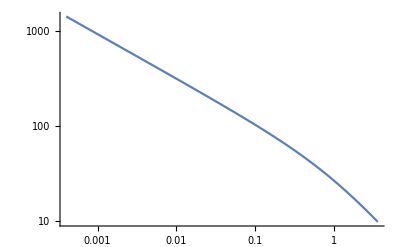

```mathematica
LogLogPlot[10^CMBdisty[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("TB"/.CosmoParams[]),1/("TR"/.CosmoParams[])},PlotRange->All]
```

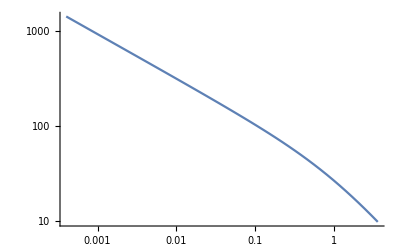

```mathematica
LogLogPlot[10^CMBdisty[["f"]][Log10[β "me"/.CosmoParams[]]],{β,1/("TB"/.CosmoParams[]),1/("TR"/.CosmoParams[])},PlotRange->All]
```

#### Compare to Neff calculation

```mathematica
(*testComputeΔNeffConstraint[ΔEtotDict_]:=Module[{gstar,ΔNeff,constraint,TDRconst},
gstar=2 (TDRt/"TR")^4/.ΔEtotDict[["params"]];(* []effective gstar for dark photon at recombination*)
ΔNeff = 8/7 (11/4)^(4/3) gstar; (*[]*)
constraint = 0.1; (*[]constraint on ΔNeff*)
TDRconst = TDRt/.Solve[ΔNeff==constraint,TDRt][[4]] ;(*[eV]upper bound on TD at recombination*)
Print[Plot[ΔEtotDict[["f"]][mDM+6],{mDM,Log10[ΔEtotDict[["mD"]][[1]]]-6,Log10[ΔEtotDict[["mD"]][[2]]]-6},PlotLabel->"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[Energy Transfered to DS] [eV]",AxesLabel->{"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[\!\(\*SubscriptBox[\(m\), \(D\)]\)] [MeV]"}]];
Print[ContourPlot[Log10[π^2/45 TDRconst^3/nDR[10^fDt,10^(mDM+6)]/.ΔEtotDict[["params"]]],{fDt,-5,0},{mDM,Log10[ΔEtotDict[["mD"]][[1]]]-6,Log10[ΔEtotDict[["mD"]][[2]]]-6},ContourLabels->True,FrameLabel->{"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[\!\(\*SubscriptBox[\(f\), \(D\)]\)] []","\!\(\*SubscriptBox[\(Log\), \(10\)]\)[\!\(\*SubscriptBox[\(m\), \(D\)]\)] [MeV]"},PlotLabel->"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[\!\(\*FractionBox[SubscriptBox[\(ρ\), SubscriptBox[\(γ\), \(D\)]], SubscriptBox[\(ρ\), \(aDM\)]]\)]"]];
Print[ContourPlot[1/2 Log10[(3TDRconst)/10^ΔEtotDict[["f"]][6+mDM] (1+π^2/45 TDRconst^3/nDR[10^fDt,10^(6+mDM)])/.ΔEtotDict[["params"]]],{fDt,-5,0},{mDM,Log10[ΔEtotDict[["mD"]][[1]]]-6,Log10[ΔEtotDict[["mD"]][[2]]]-6},ContourLabels->True,PlotLabel->"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[κ] [] - \!\(\*SubscriptBox[\(ΔN\), \(eff\)]\) bound",FrameLabel->{"\!\(\*SubscriptBox[\(Log\), \(10\)]\)[\!\(\*SubscriptBox[\(f\), \(D\)]\)] []","\!\(\*SubscriptBox[\(Log\), \(10\)]\)[\!\(\*SubscriptBox[\(m\), \(D\)]\)] [MeV]"}]]
(*Print[ContourPlot[1/2Log10[(3TDRconst)/10^ΔEtotDict[["f"]][6+mDM](1+π^2/45TDRconst^3/nDR[10^fDt,10^(6+mDM)])],{fDt,-5,0},{mDM,Log10[10^-3 me]-6,Log10[10^4 me]-6},ContourLabels->True,PlotLabel->"Subscript[Log, 10][κ] [] - Subscript[ΔN, eff] bound",FrameLabel->{"Subscript[Log, 10][Subscript[f, D]] []","Subscript[Log, 10][Subscript[m, D]] [MeV]"}]]*)
]*)
```

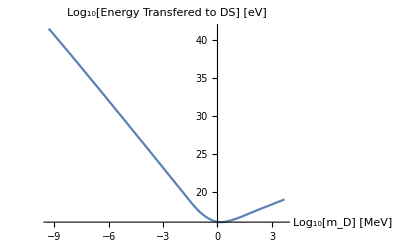

-Graphics-

-Graphics-

```mathematica
(*testComputeΔNeffConstraint[testΔEdict]*)
```

after realizing I didn’t fix to mpD

-Graphics-

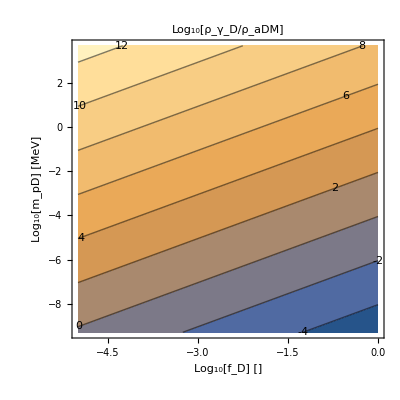

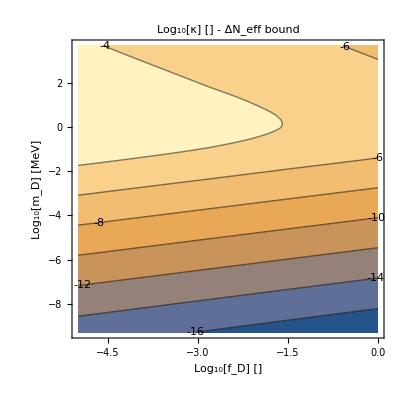

```mathematica
ComputeΔNeffConstraint[testΔEdict,10^9]
```

```mathematica
ComputeΔNeffConstraint[testΔEdict,10^9]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

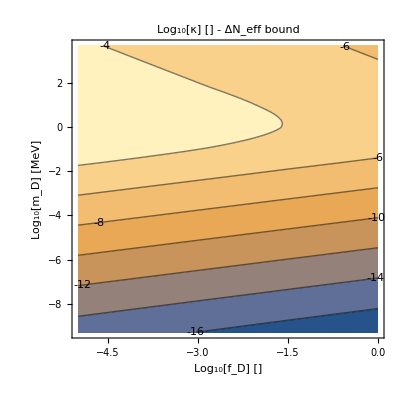

```mathematica
ComputeΔNeffConstraint[testΔEdictkis0,10^9]
```

Compute Neff bound at the point we want - Note, I missed the 10^9 in nDR (I was using mDM instead)

```mathematica
Block[{gstar,ΔNeff,constraint,TDRconst,ΔEtotDict},
ΔEtotDict=testΔEdict;
gstar=2 (TDRt/"TR")^4/.ΔEtotDict[["params"]];(* []effective gstar for dark photon at recombination*)
ΔNeff = 8/7 (11/4)^(4/3) gstar; (*[]*)
constraint = 0.1; (*[]constraint on ΔNeff*)
Print[ΔNeff];
TDRconst = TDRt/.Solve[ΔNeff==constraint,TDRt][[4]] 
]
```

1539.81 TDRt^4

0.0897704

```mathematica
0.1(2 8/7 (11/4)^(4/3))^-1
```

0.0113554

```mathematica
(1539.8133919668967)^-1
```

0.000649429

```mathematica
Block[{ΔEtotDict,logκ},
ΔEtotDict=testΔEdict;logκ=1/2 Log10[(3TDRconst)/10^ΔEtotDict[["f"]][6+mDM] (1+π^2/45 TDRconst^3/nDR[10^fDt,2 10^3"me"/.CosmoParams[]])/.ΔEtotDict[["params"]]]/.TDRconst->0.09/.mDM->0/.fDt->-2;
10^logκ
]
```

0.000156729

Compute Neff using the bound from CMB Distortion

```mathematica
Block[{ΔEtotDict,TDRtemp,logκ},
ΔEtotDict=testΔEdict;
 TDRtemp=TDRt/.Solve[1/4(TDRt/"TR")^4==1.5 10^-5,TDRt][[4]]/.CosmoParams[];

(*Print[4 1.5 10^-5("TR")^4/.CosmoParams[]];*)logκ=1/2 Log10[(3TDRconst)/10^ΔEtotDict[["f"]][6+mDM] (1+π^2/45 TDRconst^3/nDR[10^fDt,2 10^3"me"/.CosmoParams[]])/.ΔEtotDict[["params"]]]/.TDRconst->TDRtemp/.mDM->0/.fDt->-2;
10^logκ
]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0.0000113346

### Scaling Sanity Checks - expand numerical results

We want to check that we have the right scalings analytically. 

So we put the initial SM energy on it’s thermal average and take the limit of small temperature compared to mass of SM electron, and with mD = m

This gives the scaling of the interaction rate near recombination.

#### Calculate d \Gamma / d E_t

```mathematica
Print["Swtich integrals by inverting the upper bound on E_t(E)"]
Solve[Et == (2 mD)/((ESM+mD)^2/(ESM^2-m^2)-1),ESM]//FullSimplify
%/.Et->0//PowerExpand
Print["So we want the positive solution"]
```

Swtich integrals by inverting the upper bound on E_t(E)

{{ESM→1/2 (Et-(√(mD (Et+2 mD) (2 m^2+Et mD)))/mD)},{ESM→(Et mD+√(mD (Et+2 mD) (2 m^2+Et mD)))/(2 mD)}}

{{ESM→-m},{ESM→m}}

So we want the positive solution

```mathematica
Print["Find the new integration bounds on E_t by evaluating E_(t+)(E) at the boundary of (m,∞) (the limits of the E integral)"]
Series[(2 mD)/((ESM+mD)^2/(ESM^2-m^2)-1),{ESM,m,1}]//Simplify
Series[(2 mD)/((ESM+mD)^2/(ESM^2-m^2)-1),{ESM,∞,1}]//Simplify
Print["so the new bounds are E_t ∈ (0,∞)"]
```

Find the new integration bounds on E_t by evaluating E_(t+)(E) at the boundary of (m,∞) (the limits of the E integral)

(4 m mD (ESM-m))/(m+mD)^2+O[ESM-m]^2

ESM-(m^2+mD^2)/(2 mD)+((m^2-mD^2)^2)/(4 mD^2 ESM)+O[1/ESM]^2

so the new bounds are E_t ∈ (0,∞)

Compute dΓ/dE_t and E_t dΓ/dE_t

```mathematica
(*Block[{PΜ,EnergyTransferPrefactor,boundsE},*)
PΜ=("ms"+ESM)^2+("ms"+(Et-ESM))^2;
EnergyTransferPrefactor = ("n0")/("T0" β)^3 1/("Z1")((4 π"α")^2 κ^2)/(mD (2 π)^3) ("g")/4 ;(* prefactor of eqn (629) of notes over nD*)
EnergyTransferIntegrand=E^(-β(ESM-m))PΜ/(Et + "Λ")^2 Et^l;
boundsE= {Et/2+1/2 √(((Et + 2 mD)(2 m^2+Et mD))/mD),∞};
(*boundsEt={0,∞ };*)
(*shorthandrepl={"ms"->(m^2+mD^2)/(2 mD),"Λ"->4π "α" (2 π "n0")/(m "T0") (1/("T0" β))^2,"Z1"->"g" ((2 π β)/m)^(-3/2)};*)
thermalrepl={"Λ"->"Λ0" (1/("T0" β))^2,"Z1"->"g" ((2 π β)/m)^(-3/2)};
Λrepl={"Λ0"->4π "α" (2 π "n0")/(m "T0")};
msrepl = {"ms"->(m^2+mD^2)/(2 mD)};
pthav=3 √2 √((2 m)/(β 2 π)); (*average thermal momentum for boltzman distributed species (ie for SM electrons)*)
EttotheldΓdEt=0-(Integrate[EnergyTransferPrefactor EnergyTransferIntegrand,ESM]/.ESM->boundsE[[1]])//Simplify(*limit as ESM->∞ of the integral is 0*)
Print["(d Γ)/(d SubscriptBox[E, t]) (per Dark Electron) is:"]
dΓdEt = EttotheldΓdEt/.l->0/.msrepl/.thermalrepl/.Λrepl
Print["E_t(d Γ)/(d SubscriptBox[E, t]) (per Dark Electron) is:"]
EtdΓdEt = EttotheldΓdEt/.l->1/.msrepl/.thermalrepl/.Λrepl
Print["Evaluate both on the average Energy Transfer"]
dΓdEtsubbed = dΓdEt/.Et->pthav^2/(2 m)//Simplify
EtdΓdEtsubbed = EtdΓdEt/.Et->pthav^2/(2 m)//Simplify
```

(g n0 α^2 ⅇ^(-1/2 (Et-2 m+√(((Et+2 mD) (2 m^2+Et mD))/mD)) β) Et^l (Et m^2 β^2+Et mD^2 β^2+mD (4+2 √(((Et+2 mD) (2 m^2+Et mD))/mD) β+(2 ms^2+2 ms Et+Et^2+2 m^2) β^2)) κ^2)/(2 T0^3 Z1 (Λ+Et)^2 mD^2 π β^6)

(d Γ)/(d SubscriptBox[E, t]) (per Dark Electron) is:

(n0 α^2 ⅇ^(-1/2 (Et-2 m+√(((Et+2 mD) (2 m^2+Et mD))/mD)) β) √(2 π) (β/m)^(3/2) (Et m^2 β^2+Et mD^2 β^2+mD (4+2 √(((Et+2 mD) (2 m^2+Et mD))/mD) β+(Et^2+2 m^2+(Et (m^2+mD^2))/mD+((m^2+mD^2)^2)/(2 mD^2)) β^2)) κ^2)/(T0^3 mD^2 (Et+(8 n0 α π^2)/(T0^3 m β^2))^2 β^6)

E_t(d Γ)/(d SubscriptBox[E, t]) (per Dark Electron) is:

(n0 α^2 ⅇ^(-1/2 (Et-2 m+√(((Et+2 mD) (2 m^2+Et mD))/mD)) β) Et √(2 π) (β/m)^(3/2) (Et m^2 β^2+Et mD^2 β^2+mD (4+2 √(((Et+2 mD) (2 m^2+Et mD))/mD) β+(Et^2+2 m^2+(Et (m^2+mD^2))/mD+((m^2+mD^2)^2)/(2 mD^2)) β^2)) κ^2)/(T0^3 mD^2 (Et+(8 n0 α π^2)/(T0^3 m β^2))^2 β^6)

Evaluate both on the average Energy Transfer

(n0 T0^3 α^2 ⅇ^(-(9-2 m π β+β √(((9 mD+2 m^2 π β) (9+2 mD π β))/(mD β^2)))/(2 π)) √(π/2) (36 m^2 mD π β+36 mD^3 π β+m^4 π^2 β^2+mD^4 π^2 β^2+2 mD^2 (81+2 π β √(((9 mD+2 m^2 π β) (9+2 mD π β))/(mD β^2))+π^2 (4+3 m^2 β^2))) κ^2)/(mD^3 √(β/m) (8 n0 α π^3+9 T0^3 m β)^2)

(9 n0 T0^3 α^2 ⅇ^(-(9-2 m π β+β √(((9 mD+2 m^2 π β) (9+2 mD π β))/(mD β^2)))/(2 π)) (36 m^2 mD π β+36 mD^3 π β+m^4 π^2 β^2+mD^4 π^2 β^2+2 mD^2 (81+2 π β √(((9 mD+2 m^2 π β) (9+2 mD π β))/(mD β^2))+π^2 (4+3 m^2 β^2))) κ^2)/(mD^3 √(2 π) β √(β/m) (8 n0 α π^3+9 T0^3 m β)^2)

```mathematica
EttotheldΓdEt[mD,m,κ,β,Et,l];
%["EttotheldΓdEt"]
%/.%%["thermalrepl"]/.%%["Λrepl"]/.%%["msrepl"]
%/.mD->m//Simplify
```

(g n0 α^2 ⅇ^(-1/2 (Et-2 m+√(((Et+2 mD) (2 m^2+Et mD))/mD)) β) Et^l (Et m^2 β^2+Et mD^2 β^2+mD (4+2 √(((Et+2 mD) (2 m^2+Et mD))/mD) β+(2 ms^2+2 ms Et+Et^2+2 m^2) β^2)) κ^2)/(2 T0^3 Z1 (Λ+Et)^2 mD^2 π β^6)

(n0 α^2 ⅇ^(-1/2 (Et-2 m+√(((Et+2 mD) (2 m^2+Et mD))/mD)) β) Et^l √(2 π) (β/m)^(3/2) (Et m^2 β^2+Et mD^2 β^2+mD (4+2 √(((Et+2 mD) (2 m^2+Et mD))/mD) β+(Et^2+2 m^2+(Et (m^2+mD^2))/mD+((m^2+mD^2)^2)/(2 mD^2)) β^2)) κ^2)/(T0^3 mD^2 (Et+(8 n0 α π^2)/(T0^3 m β^2))^2 β^6)

(n0 T0^3 α^2 ⅇ^(-1/2 (Et-2 m+√((Et+2 m)^2)) β) Et^l √(2 π) √(β/m) (4+2 √((Et+2 m)^2) β+(Et+2 m)^2 β^2) κ^2)/(β (8 n0 α π^2+T0^3 Et m β^2)^2)

```mathematica
Print["n_0/T_0^3 and β m_e (at recombination) are small and large (respectively) dimensionless numbers"]
("n0")/("T0")^3/.CosmoParams[]
("me")/("TR")/.CosmoParams[]
Print["Expand (d Γ)/(d SubscriptBox[E, t]) and E_t(d Γ)/(d SubscriptBox[E, t]) (per dark electron) to leading order in both n_0/T_0^3 and β m_e"]
dΓdEtexpanded=(Series[Series[dΓdEtsubbed/."n0"->ξn ("T0")^3,{ξn,0,1}]/.β->ξβ/m,{ξβ,∞,1}]//Normal)/.{ξβ->β m,ξn->("n0")/("T0")^3}//PowerExpand//Simplify
EtdΓdEtexpanded=(Series[Series[EtdΓdEtsubbed/."n0"->ξn ("T0")^3,{ξn,0,1}]/.β->ξβ/m,{ξβ,∞,2}]//Normal)/.{ξβ->β m,ξn->("n0")/("T0")^3}//PowerExpand//Simplify
```

n_0/T_0^3 and β m_e (at recombination) are small and large (respectively) dimensionless numbers

1.2641×10^-10

1.81818×10^6

Expand (d Γ)/(d SubscriptBox[E, t]) and E_t(d Γ)/(d SubscriptBox[E, t]) (per dark electron) to leading order in both n_0/T_0^3 and β m_e

(n0 α^2 ⅇ^(-(9 (m+mD)^2 (18 m mD-9 mD^2+m^2 (-9+8 mD π β)))/(32 m^3 mD^2 π^2 β)) (m^4+6 m^2 mD^2+mD^4) π^(5/2) κ^2)/(81 √2 T0^3 m^(3/2) mD^3 √β)

(n0 α^2 ⅇ^(-(9 (m+mD)^2 (-162 m mD^3+81 mD^4-18 m^2 mD^2 (-9+2 mD π β)+18 m^3 mD (-9+4 mD π β)+m^4 (81-36 mD π β+32 mD^2 π^2 β^2)))/(128 m^5 mD^3 π^3 β^2)) (m^4+6 m^2 mD^2+mD^4) π^(3/2) κ^2)/(9 √2 T0^3 m^(3/2) mD^3 β^(3/2))

```mathematica
Print["Evaluate expansions of dΓ/dE_t and E_tdΓ/dE_t (per dark electron) at m_D=m=m_e at recombination"]
Print["Expanded dΓ/dE_t is:"]
dΓdEtexpanded/.mD->m//Simplify
%/.{m->"me",β->1/("TR")}/.CosmoParams[]
Print["This gives the back of the envelope κ constraint from CMB distortion"]
κ<=√((10^-4(H[1/("TR")]/.CosmoParams[]))/(%%)κ^2)
Print["Expanded E_tdΓ/dE_t is:"]
EtdΓdEtexpanded/.mD->m//Simplify
%/.{m->"me",β->1/("TR")}/.CosmoParams[]
```

Evaluate expansions of dΓ/dE_t and E_tdΓ/dE_t (per dark electron) at m_D=m=m_e at recombination

Expanded dΓ/dE_t is:

(4 √2 n0 α^2 ⅇ^(-9/π) π^(5/2) κ^2)/(81 T0^3 √m √β)

3.47796×10^-19 κ^2

This gives the back of the envelope κ constraint from CMB distortion

κ≤1.01695×10^-7

Expanded E_tdΓ/dE_t is:

(4 √2 n0 α^2 ⅇ^(-9/π) π^(3/2) κ^2)/(9 T0^3 √m β^(3/2))

2.74×10^-19 κ^2

```mathematica
Print["The values of these expressions per SM electron are related by n_D0/n_0. This is an order 1 constant."]
Print["Eg. for m_p_D=m_p, f_D=0.01 we have for the ratio:"]
DarktoSMnratio=nD0[0.01,10^9]/("n0")/.CosmoParams[];
Subscript[n, D0]/Subscript[n, 0]==DarktoSMnratio
Print["This affects the bounds for our rough estimate as"]
DarktoSMnratio dΓdEtexpanded/.mD->m//Simplify
%/.{m->"me",β->1/("TR")}/.CosmoParams[]
Print["This gives the back of the envelope κ constraint from CMB distortion"]
κ<=√((10^-4(H[1/("TR")]/.CosmoParams[]))/(%%)κ^2)
Print["Which only changes the κ bound by about a factor of 4"]
```

The values of these expressions per SM electron are related by n_D0/n_0. This is an order 1 constant.

Eg. for m_p_D=m_p, f_D=0.01 we have for the ratio:

n_D0/n_0==0.054027

This affects the bounds for our rough estimate as

(0.00376195 n0 α^2 κ^2)/(T0^3 √m √β)

1.87904×10^-20 κ^2

This gives the back of the envelope κ constraint from CMB distortion

κ≤4.37514×10^-7

Which only changes the κ bound by about a factor of 4

```mathematica
"Λ"/.thermalrepl/.Λrepl
```

(8 n0 α π^2)/(T0^3 m β^2)

In the case of m_e_D=m_e we have the simple expression for E_t^ldΓ/dE_t

(g n0 α^2 ⅇ^(-Et β) Et^l (4+2 (Et+2 m) β+(Et+2 m)^2 β^2) κ^2)/(2 T0^3 Z1 (Λ+Et)^2 m π β^6)

(n0 α^2 ⅇ^(-Et β) Et^l √(2 π) (β/m)^(3/2) (4+2 (Et+2 m) β+(Et+2 m)^2 β^2) κ^2)/(T0^3 m (Et+Λ0/(T0^2 β^2))^2 β^6)

This expression goes as E_te^(-SubscriptBox[E, t] β) Μ^2 ( where Μ^2=(SuperscriptBox[s, 2] + SuperscriptBox[u, 2])/(t + Λ)^2 ) and has the scalings:

E_t - for E_t << Λ (Μ constant from screening, no Boltz suppression)
E_t^-1 - for Λ << E_t << β (Μ ~ E_t^-2, no Boltz suppression) 
E_t^-1 e^(-SubscriptBox[E, t] β) - for T << E_t << m (Μ ~ E_t^-2, with Boltz suppression) 
E_t e^(-SubscriptBox[E, t] β) - for m << E_t (u ~ t ~ E_t so Μ constant, with Boltz suppression)

The plot for E_tdΓ/dE_t is peaked around the screening energy Λ

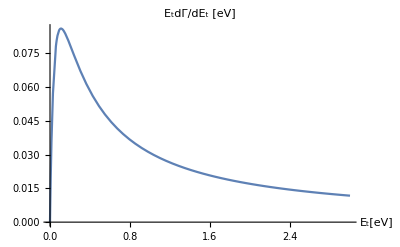

Λ==1.10191×10^-17

Above Λ and below T, it falls off as ~ E_t^-1 (as in the appendix calculation)

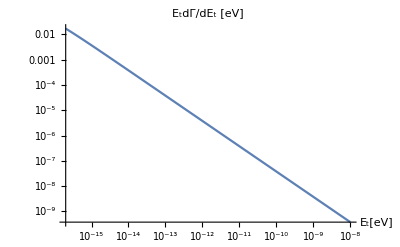

At E_t ~ T it begins to fall off exponentially

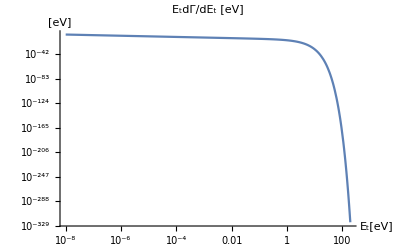

```mathematica
Print["In the case of m_e_D=m_e we have the simple expression for E_t^ldΓ/dE_t"]
EttotheldΓdEt/.msrepl/.mD->m//Simplify//PowerExpand
%/.thermalrepl
Print["This expression goes as E_te^(-SubscriptBox[E, t] β) Μ^2 ( where Μ^2=(SuperscriptBox[s, 2] + SuperscriptBox[u, 2])/(t + Λ)^2 ) and has the scalings:\n\nE_t - for E_t << Λ (Μ constant from screening, no Boltz suppression)\nE_t^-1 - for Λ << E_t << β (Μ ~ E_t^-2, no Boltz suppression) \nE_t^-1 e^(-SubscriptBox[E, t] β) - for T << E_t << m (Μ ~ E_t^-2, with Boltz suppression) \nE_t e^(-SubscriptBox[E, t] β) - for m << E_t (u ~ t ~ E_t so Μ constant, with Boltz suppression)"]
Print["The plot for E_tdΓ/dE_t is peaked around the screening energy Λ"]
Plot[EtdΓdEt/.mD->m/.m->"me"/.CosmoParams[]/.κ->1/.β->1/("TR")/.CosmoParams[],{Et,0,3 10^-16},PlotRange->All,PlotLabel->"E_tdΓ/dE_t [eV]",AxesLabel->{"E_t[eV]"}]
Λ==("Λ"/.thermalrepl/.Λrepl/.β->1/("TR")/.m->"me"/.CosmoParams[])
Print["Above Λ and below T, it falls off as ~ E_t^-1 (as in the appendix calculation)"]
LogLogPlot[EtdΓdEt/.mD->m/.m->"me"/.CosmoParams[]/.κ->1/.β->1/("TR")/.CosmoParams[],{Et,2 10^-16, 10^-8},PlotLabel->"E_tdΓ/dE_t [eV]",AxesLabel->{"E_t[eV]"}]
Print["At E_t ~ T it begins to fall off exponentially"]
LogLogPlot[EtdΓdEt/.mD->m/.m->"me"/.CosmoParams[]/.κ->1/.β->1/("TR")/.CosmoParams[],{Et,10^-8,5 10^3},PlotRange->All,PlotLabel->"E_tdΓ/dE_t [eV]",AxesLabel->{"E_t[eV]","[eV]"}]
```

The plot for dΓ/dE_t is nearly flat until Λ

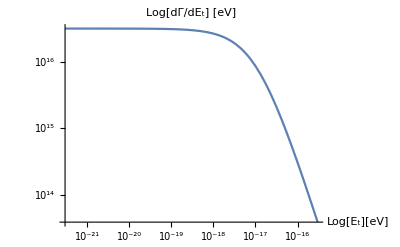

Λ==1.10191×10^-17

Away from the Λ, it falls off exponentially as we'd expect

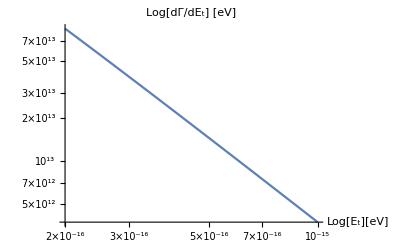

```mathematica
Print["The plot for dΓ/dE_t is nearly flat until Λ"]
LogLogPlot[dΓdEt/.mD->m/.m->"me"/.CosmoParams[]/.κ->1/.β->1/("TR")/.CosmoParams[],{Et,3 10^-22,3 10^-16},PlotRange->All,PlotLabel->"Log[dΓ/dE_t] [eV]",AxesLabel->{"Log[E_t][eV]"}]
(*Plot[dΓdEt/.mD->m/.m->"me"/.CosmoParams[]/.κ->1/.β->1/("TR")/.CosmoParams[],{Et,3 10^-22,3 10^-17},PlotRange->All,PlotLabel->"dΓ/dE_t [eV]",AxesLabel->{"E_t[eV]"}]*)
Λ==("Λ"/.thermalrepl/.Λrepl/.β->1/("TR")/.m->"me"/.CosmoParams[])
Print["Away from the Λ, it falls off exponentially as we'd expect"]
LogLogPlot[dΓdEt/.mD->m/.m->"me"/.CosmoParams[]/.κ->1/.β->1/("TR")/.CosmoParams[],{Et,2 10^-16, 10^-15},PlotLabel->"Log[dΓ/dE_t] [eV]",AxesLabel->{"Log[E_t][eV]"}]
```

```mathematica
Print["compare the analytic estimates to the integral expressions used in the full calculation of N_eff and CMB y-type distortion."]
Print["dE_t/(d a) is (same parameters as above)"]
dEtda=ESMIntegral["me"/.CosmoParams[],"me"/.CosmoParams[],1,("me")/("TR")/.CosmoParams[],CosmoParams[],1]
Print["Γ is (same parameters as above)"]
Γ=ESMIntegral["me"/.CosmoParams[],"me"/.CosmoParams[],1,("me")/("TR")/.CosmoParams[],CosmoParams[],0]
```

compare the analytic estimates to the integral expressions used in the full calculation of N_eff and CMB y-type distortion.

dE_t/(d a) is (same parameters as above)

4.19047×10^15

Γ is (same parameters as above)

0.343709

```mathematica
Print["Comparing to the plots of E_t dΓ/dE_t given above, this value is reasonable"]
dEtdt=dEtda aH[1/("TR")]/.CosmoParams[]
Print["Similarily for dΓ/dE_t"]
Γ
```

Comparing to the plots of E_t dΓ/dE_t given above, this value is reasonable

1.37022×10^-16

Similarily for dΓ/dE_t

0.343709

```mathematica
Print["Why are we peaked around the screening length instead of the mean energy of the electrons?"]
(*Series[EttotheldΓdEt/.l->1/.Et->ξEt Λ,{ξEt,0,1}] //PowerExpand// Simplify*)
EttotheldΓdEt /.msrepl/.mD->m//Simplify//PowerExpand
EtdΓdEt /.mD->m//Simplify//PowerExpand
Print["From this expression for E_t dΓ/dt, we see that the leading power in large E_t varies as"]
E^(-β Et)Et^3/(Et + Λ)^2
E^(-β Et)(Et(1+Et β+Et^2 β^2))/(Et + Λ)^2
Plot[%/.Λ->10^-17/.β->1/("TR")/.CosmoParams[],{Et,0,10^-16}]
```

Why are we peaked around the screening length instead of the mean energy of the electrons?

(g n0 α^2 ⅇ^(-Et β) Et^l (4+2 (Et+2 m) β+(Et+2 m)^2 β^2) κ^2)/(2 T0^3 Z1 (Λ+Et)^2 m π β^6)

(n0 T0^3 α^2 ⅇ^(-Et β) Et √(2 π) (4+2 (Et+2 m) β+(Et+2 m)^2 β^2) κ^2)/(√m √β (8 n0 α π^2+T0^3 Et m β^2)^2)

From this expression for E_t dΓ/dt, we see that the leading power in large E_t varies as

(ⅇ^(-Et β) Et^3)/(Et+Λ)^2

(ⅇ^(-Et β) Et (1+Et β+Et^2 β^2))/(Et+Λ)^2

-Graphics-

### Boltzmann Equation Unit testing

#### Until when does the photon entropy density dominate over matter?

```mathematica
sγ = 4/3 π^2/90 "gstar" T^3/.CosmoParams[]
se = ("me")/T("n0")/("T0")^3 T^3/.CosmoParams[]
```

0.494211 T^3

0.0000632051 T^2

```mathematica
Solve[sγ T == se T,T]
```

{{T→0.},{T→0.},{T→0.},{T→0.000127891}}

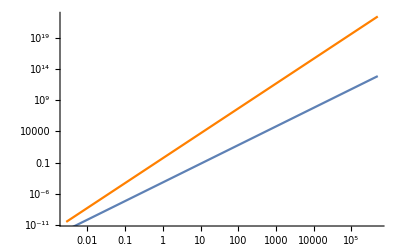

```mathematica
Show[{LogLogPlot[sγ T,{T,"Td"/.CosmoParams[],("TR")/10^2/.CosmoParams[]},PlotStyle->Orange],LogLogPlot[se  T,{T,"Td"/.CosmoParams[],("TR")/10^2/.CosmoParams[]}]}]
```

```mathematica
Print["Upshot here is I we need to include the baryon energy density here in the SM."]
```

#### DS Energy Density Boltzmann Numerical Evolution Unit Testing - Just DS

As in the above sections, we make the assumption that m_e_D=m_e and m_p_D=m_p, we also take f_D=0.01

```mathematica
EttotheldΓdEt[mD,m,κ,β,Et,l];
%["EttotheldΓdEt"]
EtdΓdEt=%/.%%["thermalrepl"]/.%%["Λrepl"]/.%%["msrepl"]/.l->1
Print["we need the source term <dE_tr/(dt dV)> the energy transfer rate per unit time and volume from the SM to the DS. The integrand of corresponding integral is simply n_D E_t dΓ/dt"]
nD EtdΓdEt/.mD->m//Simplify//PowerExpand
Print["We can substitute an expression for nD in terms of cosmo and model parameters"]
%%/.nD->nD0[fD,mpD]/(("T0")^3 β^3)
Print["We then substitute numerical values for the parameters and define a function for the integral of this expression which gives <dE_tr/(dt dV)>"]
NdEtrbydtdVintegrand= %%/.m->"me"/.κ->1/.{fD->0.01,mpD->2000"me"}/.CosmoParams[]
dEtrbydtdV[βt_?NumberQ]:=NIntegrate[NdEtrbydtdVintegrand/.β->βt,{Et,0,∞}]
```

(g n0 α^2 ⅇ^(-1/2 (Et-2 m+√(((Et+2 mD) (2 m^2+Et mD))/mD)) β) Et^l (Et m^2 β^2+Et mD^2 β^2+mD (4+2 √(((Et+2 mD) (2 m^2+Et mD))/mD) β+(2 ms^2+2 ms Et+Et^2+2 m^2) β^2)) κ^2)/(2 T0^3 Z1 (Λ+Et)^2 mD^2 π β^6)

1/(T0^3 mD^2 (Et+(8 n0 α π^2)/(T0^3 m β^2))^2 β^6)n0 α^2 ⅇ^(-1/2 (Et-2 m+√(((Et+2 mD) (2 m^2+Et mD))/mD)) β) Et √(2 π) (β/m)^(3/2) (Et m^2 β^2+Et mD^2 β^2+mD (4+2 √(((Et+2 mD) (2 m^2+Et mD))/mD) β+(Et^2+2 m^2+(Et (m^2+mD^2))/mD+((m^2+mD^2)^2)/(2 mD^2)) β^2)) κ^2

we need the source term <dE_tr/(dt dV)> the energy transfer rate per unit time and volume from the SM to the DS. The integrand of corresponding integral is simply n_D E_t dΓ/dt

(n0 T0^3 α^2 ⅇ^(-Et β) Et nD √(2 π) (4+2 (Et+2 m) β+(Et+2 m)^2 β^2) κ^2)/(√m √β (8 n0 α π^2+T0^3 Et m β^2)^2)

We can substitute an expression for nD in terms of cosmo and model parameters

(n0 α^2 ρDM0 ⅇ^(-Et β) Et fD √(2 π) (4+2 (Et+2 m) β+(Et+2 m)^2 β^2) κ^2)/(√m mpD β^(7/2) (8 n0 α π^2+T0^3 Et m β^2)^2)

We then substitute numerical values for the parameters and define a function for the integral of this expression which gives <dE_tr/(dt dV)>

(3.98088×10^-50 ⅇ^(-Et β) Et (4+2 (1000000+Et) β+(1000000+Et)^2 β^2))/(β^(7/2) (1.13834×10^-21+7.8125×10^-6 Et β^2)^2)

```mathematica
dEtrbydtdV[("Td")^-1/.CosmoParams[]]
dEtrbydtdV[("TR")^-1/.CosmoParams[]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Et near {Et} = {259788.}. NIntegrate obtained 966292. and 421.621 for the integral and error estimates.

966292.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Et near {Et} = {1.9984×10^-15}. NIntegrate obtained 1.95368×10^-29 and 2.88913×10^-32 for the integral and error estimates.

1.95368×10^-29

```mathematica
(*ρD[β_]:= ("me"+2000 "me")nD0[0.01,10^9]/(("T0")^3 β^3)+ ργD[β]/.CosmoParams[]*)
```

```mathematica
Clear[EttotheldΓdEt]
```

Solve for the evolution of the energy density in the dark sector. Use the initial condition that DS Temperature is 0, and take κ=10^-5. 

Note we assume the DS is radiation dominated so that 3(ρ_D+P_D)=4ρ_D

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Et near {Et} = {259788.}. NIntegrate obtained 966292. and 421.621 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ρDt→InterpolatingFunction[…]}}

Plot the solution (dark energy density)

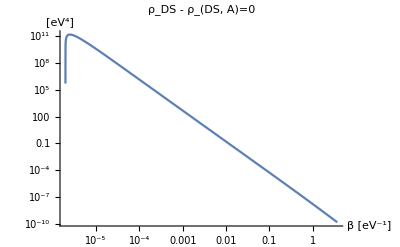

Plot the comoving energy density (assuming DS is radiation dominated)

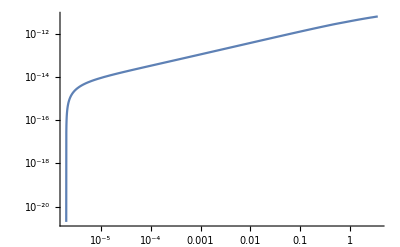

```mathematica
Clear[ρD]
Print["Solve for the evolution of the energy density in the dark sector. Use the initial condition that DS Temperature is 0, and take κ=10^-5. \n\nNote we assume the DS is radiation dominated so that 3(ρ_D+P_D)=4ρ_D "]
ρD=NDSolve[{(("T0")/aH[β](κ^2 dEtrbydtdV[β]-4H[β] ρDt[β])/.CosmoParams[]/.κ->10^-5)==ρDt'[β] ,ρDt[1/("Td")/.CosmoParams[]]==0},ρDt,{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]}]
Print["Plot the solution (dark energy density)"]
LogLogPlot[(ρDt/.ρD[[1]])[β],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotRange->All,PlotLabel->"ρ_DS - ρ_(DS, A)=0",AxesLabel->{"β [eV^-1]","[eV^4]"}]
Print["Plot the comoving energy density (assuming DS is radiation dominated)"]
LogLogPlot[("T0"β^4/.CosmoParams[])(ρDt/.ρD[[1]])[β],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotRange->All]
```

```mathematica
Print["The DS energy at recombination is then"]
(ρDt/.ρD[[1]])[("TR")^-1/.CosmoParams[]]
Print["We can solve for the corresponding DS temperature (and check our assumption that the DS is radiation dominated)"]
TDsol=NSolve[3 TD (nDR[0.01,10^9]+π^2/45 TD^3/.CosmoParams[])==(ρDt/.ρD[[1]])[("TR")^-1/.CosmoParams[]],TD][[4]]
Print["The ratio of matter to radiation ρ_m/ρ_r is:"]
(3 TD (nDR[0.01,10^9]))/(3 TD (π^2/45 TD^3))/.CosmoParams[]/.TDsol
Print["So our approximation of a radiation dominated dark sector is entirely valid. \n\nNow compute N_eff given our DS temperature"]
gstar=2 (TD/"TR")^4/.TDsol/.CosmoParams[];(* []effective gstar for dark photon at recombination*)
ΔNeff = 8/7 (11/4)^(4/3) gstar(*[]*)
```

The DS energy at recombination is then

1.53078×10^-9

We can solve for the corresponding DS temperature (and check our assumption that the DS is radiation dominated)

{TD→0.00694506}

The ratio of matter to radiation ρ_m/ρ_r is:

1.9332×10^-6

So our approximation of a radiation dominated dark sector is entirely valid. 

Now compute N_eff given our DS temperature

3.58238×10^-6

Be wary however that it seems the NSolve is unstable above κ=10^-4.5. We can see reasonable scaling with κ here. κ ∈ {10^-4.5,10^-5,10^-5.5}

{{ρDt→InterpolatingFunction[…]}}

{{ρDt→InterpolatingFunction[…]}}

{{ρDt→InterpolatingFunction[…]}}

Plot the solution (dark energy density)

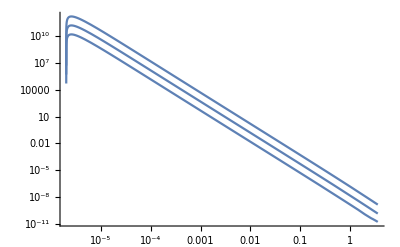

```mathematica
Print["Be wary however that it seems the NSolve is unstable above κ=10^-4.5. We can see reasonable scaling with κ here. κ ∈ {10^-4.5,10^-5,10^-5.5}"]
ρD4p5=NDSolve[{(("T0")/aH[β](κ^2 dEtrbydtdV[β]-4H[β] ρDt[β])/.CosmoParams[]/.κ->10^-4.5)==ρDt'[β] ,ρDt[1/("Td")/.CosmoParams[]]==0},ρDt,{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]}]
ρD5=NDSolve[{(("T0")/aH[β](κ^2 dEtrbydtdV[β]-4H[β] ρDt[β])/.CosmoParams[]/.κ->10^-5)==ρDt'[β] ,ρDt[1/("Td")/.CosmoParams[]]==0},ρDt,{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]}]
ρD5p5=NDSolve[{(("T0")/aH[β](κ^2 dEtrbydtdV[β]-4H[β] ρDt[β])/.CosmoParams[]/.κ->10^-5.5)==ρDt'[β] ,ρDt[1/("Td")/.CosmoParams[]]==0},ρDt,{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]}]
Print["Plot the solution (dark energy density)"]
Show[{LogLogPlot[(ρDt/.ρD4p5[[1]])[β],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotRange->All],
LogLogPlot[(ρDt/.ρD5[[1]])[β],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotRange->All],
LogLogPlot[(ρDt/.ρD5p5[[1]])[β],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotRange->All]}]
```

Compare to SM photon energy density

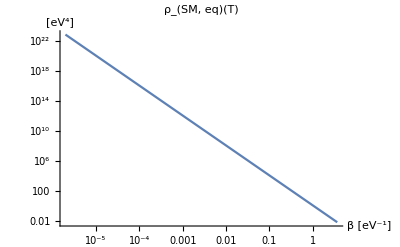

```mathematica
Print["Compare to SM photon energy density"]
LogLogPlot[π^2/30 3.4 β^-4,{β,("Td")^-1/.CosmoParams[],("TR")^-1/.CosmoParams[]},PlotLabel->"ρ_(SM, eq)(T)",AxesLabel->{"β [eV^-1]","[eV^4]"}]
```

Solve for the evolution of the energy density in the dark sector. Use the initial condition that the first derivative at decoupling is 0, and take κ=10^-5. 

Note we assume the DS is radiation dominated so that 3(ρ_D+P_D)=4ρ_D

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Et near {Et} = {259788.}. NIntegrate obtained 966292. and 421.621 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ρDt→InterpolatingFunction[…]}}

Plot the solution (dark energy density)

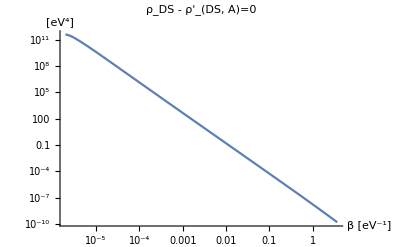

Plot the comoving energy density (assuming DS is radiation dominated)

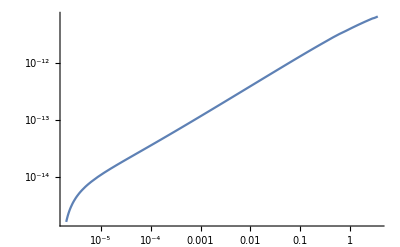

```mathematica
Clear[ρD]
Print["Solve for the evolution of the energy density in the dark sector. Use the initial condition that the first derivative at decoupling is 0, and take κ=10^-5. \n\nNote we assume the DS is radiation dominated so that 3(ρ_D+P_D)=4ρ_D "]
ρD=NDSolve[{(("T0")/aH[β](κ^2 dEtrbydtdV[β]-4H[β] ρDt[β])/.CosmoParams[]/.κ->10^-5)==ρDt'[β] ,ρDt'[1/("Td")/.CosmoParams[]]==0},ρDt,{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]}]
Print["Plot the solution (dark energy density)"]
LogLogPlot[(ρDt/.ρD[[1]])[β],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotRange->All,PlotLabel->"ρ_DS - ρ'_(DS, A)=0",AxesLabel->{"β [eV^-1]","[eV^4]"}]
Print["Plot the comoving energy density (assuming DS is radiation dominated)"]
LogLogPlot[("T0"β^4/.CosmoParams[])(ρDt/.ρD[[1]])[β],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotRange->All]
```

Now try evolving from a much earlier time (10^7 GeV)and with the initial condition used in the paper that \rho_{DS}'=0 there

Solve for the evolution of the energy density in the dark sector. Use the initial condition that the first derivative at decoupling is 0, and take κ=10^-4.5. 

Note we assume the DS is radiation dominated so that 3(ρ_D+P_D)=4ρ_D

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Et near {Et} = {2.17598×10^6}. NIntegrate obtained 2.4483×10^11 and 1.11063×10^7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ρDt→InterpolatingFunction[…]}}

Plot the solution (dark energy density)

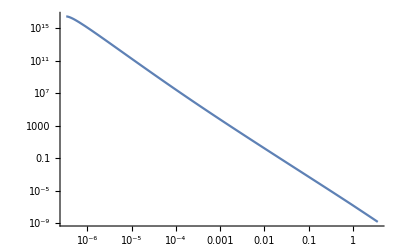

Plot the comoving energy density (assuming DS is radiation dominated)

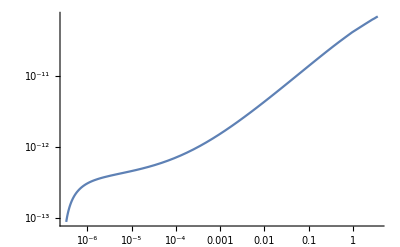

```mathematica
Clear[ρD]
Print["
Now try evolving from a much earlier time (10^7 GeV)and with the initial condition used in the paper that \rho_{DS}'=0 there

Solve for the evolution of the energy density in the dark sector. Use the initial condition that the first derivative at decoupling is 0, and take κ=10^-4.5. \n\nNote we assume the DS is radiation dominated so that 3(ρ_D+P_D)=4ρ_D "]
Ti = 3 10^6 ;(*10^7 GeV, where the process that populates the DS photon bath becomes efficient*)
ρD=NDSolve[{(("T0")/aH[β](κ^2 dEtrbydtdV[β]-4H[β] ρDt[β])/.CosmoParams[]/.κ->10^-4.5)==ρDt'[β] ,ρDt'[1/Ti]==0},ρDt,{β,1/Ti,1/("TR")/.CosmoParams[]}]
Print["Plot the solution (dark energy density)"]
LogLogPlot[(ρDt/.ρD[[1]])[β],{β,1/Ti,1/("TR")/.CosmoParams[]},PlotRange->All]
Print["Plot the comoving energy density (assuming DS is radiation dominated)"]
LogLogPlot[("T0"β^4/.CosmoParams[])(ρDt/.ρD[[1]])[β],{β,1/Ti,1/("TR")/.CosmoParams[]},PlotRange->All]
```

#### Solve for SM energy density as a function of time

```mathematica
π^2/30 3.38(("Td")^4/.CosmoParams[])
((√((8 π)/(3 ("Mp")^2))ρSMt[t]^(1/2))/.CosmoParams[]/.κ->10^-4.5/."Mp"->1.22 10^19 10^9)/.ρSMt[t]->%
H[("Td")^-1]/.CosmoParams[]
Print["This shows that our expression for parametrized hubble is approximately the one used in the milicharge paper"]
```

6.94985×10^22

6.25442×10^-17

5.87598×10^-17

This shows that our expression for parametrized hubble is approximately the one used in the milicharge paper

Compare to SM photon energy density

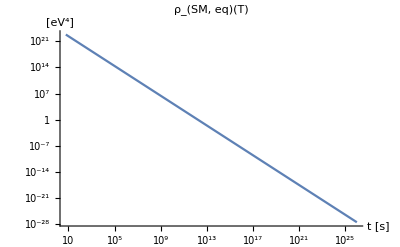

```mathematica
Print["Compare to SM photon energy density"]
LogLogPlot[π^2/30 3.4 (("Td")^4/.CosmoParams[])36(t)^-2,{t,6,10^26},PlotLabel->"ρ_(SM, eq)(T)",AxesLabel->{"t [s]","[eV^4]"}]
```

```mathematica
DSolve[{ρ'[a]==-4  1/a ρ[a],ρ[c]==b},ρ[a],a][[1]]
```

{ρ[a]→(b c^4)/a^4}

```mathematica
DSolve[{ρ'[t]==t^-1 a ρ[t],ρ[c]==b},ρ[t],t][[1]]
%/.a √b c->a √b c+2//Simplify
%/.b->(√(π^2/30 3.38(("Td")^4/.CosmoParams[])))^2/.c->6/.A->-4 √((8 π)/(3 ("Mp")^2))/."Mp"->1.22 10^19 10^9//Simplify
```

{ρ[t]→b c^-a t^a}

{ρ[t]→b c^-a t^a}

{ρ[t]→(6.94985×10^22)/(t^(9.48985×10^-28))}

```mathematica
DSolve[{ρ'[t]==a ρ[t]^(3/2),ρ[c]==b},ρ[t],t][[1]]
%/.a √b c->a √b c+2//Simplify
%/.b->(√(π^2/30 3.38(("Td")^4/.CosmoParams[])))^2/.c->6/.a->-4 √((8 π)/(3 ("Mp")^2))/."Mp"->1.22 10^19 10^9//Simplify
```

{ρ[t]→(4 b)/(-2+a √b c-a √b t)^2}

{ρ[t]→4/(a^2 (c-t)^2)}

{ρ[t]→(4.44162×10^54)/(-6.+t)^2}

```mathematica
Print["Solve for the evolution of the energy density in the dark sector. Use the initial condition that the first derivative at decoupling is 0, and take κ=10^-4.5. \n\nNote we assume the DS is radiation dominated so that 3(ρ_D+P_D)=4ρ_D "]
ρSM=NDSolve[{((-κ^2 dEtrbydtdV[(30/(π^2 3.38)ρSMt[t])^(-1/4)]-4 √((8 π)/(3 ("Mp")^2))ρSMt[t]^(3/2))/.CosmoParams[]/.κ->10^-4.5/."Mp"->1.22 10^19 10^9)==ρSMt'[t] ,ρSMt[6]==π^2/30 3.38(("Td")^4/.CosmoParams[])},ρSMt,{t,6,10^26}]
Print["Plot the solution (SM energy density)"]
LogLogPlot[(ρSMt/.ρSM[[1]])[t],{t,6,10^26},PlotRange->Full](*PlotRange->{{0,10^26},{0,10^23}}]*)
Print["Plot the comoving energy density (assuming DS is radiation dominated) using a = const. t^(1/2)"]
LogLogPlot[(t^2)(ρSMt/.ρSM[[1]])[t],{t,6,10^26},PlotRange->Full]
Print["We see that the energy transfer is so weak, that it does not affect the comoving energy density at all."]
```

```mathematica
(ρSMt/.ρSM[[1]])[0]
```

6.94985×10^22

```mathematica
3600 24 365 1000 300//N
```

9.4608×10^12

```mathematica
Clear[ρD]
Print["Solve for the evolution of the energy density in the dark sector. Use the initial condition that the first derivative at decoupling is 0, and take κ=10^-4.5. \n\nNote we assume the DS is radiation dominated so that 3(ρ_D+P_D)=4ρ_D "]
ρSM=NDSolve[{((-κ^2("T0")/aH[(30/(π^2 3.38)ρSMt[a])^(-1/4)] dEtrbydtdV[(30/(π^2 3.38)ρSMt[a])^(-1/4)]+-4/a ρSMt[a])/.CosmoParams[]/.κ->10^-4.5)==ρSMt'[a] ,ρSMt[10^-9]==π^2/30 3.38(("Td")^4/.CosmoParams[])},ρSMt,{a,10^-9,10^-3}]
```

Solve for the evolution of the energy density in the dark sector. Use the initial condition that the first derivative at decoupling is 0, and take κ=10^-4.5. 

Note we assume the DS is radiation dominated so that 3(ρ_D+P_D)=4ρ_D

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Et near {Et} = {259788.}. NIntegrate obtained 966292. and 421.621 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{ρSMt→InterpolatingFunction[…]}}

Plot the solution (SM energy density)

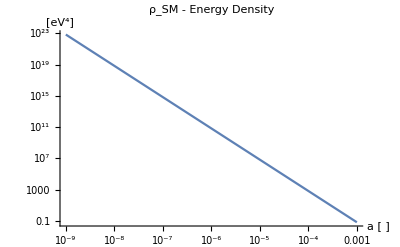

Plot the comoving energy density (assuming DS is radiation dominated) using a = const. t^(1/2)

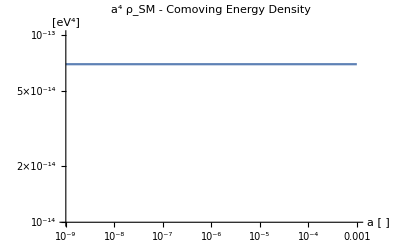

We see that the energy transfer is so weak, that it does not affect the comoving energy density at all.

```mathematica
Print["Plot the solution (SM energy density)"]
LogLogPlot[(ρSMt/.ρSM[[1]])[a],{a,10^-9,10^-3},PlotRange->Full,PlotLabel->"ρ_SM - Energy Density",AxesLabel->{"a [ ]","[eV^4]"}](*PlotRange->{{0,10^26},{0,10^23}}]*)
Print["Plot the comoving energy density (assuming DS is radiation dominated) using a = const. t^(1/2)"]
LogLogPlot[(a^4)(ρSMt/.ρSM[[1]])[a],{a,10^-9,10^-3},PlotRange->{10^-14,10^-13},PlotLabel->"a^4 ρ_SM - Comoving Energy Density",AxesLabel->{"a [ ]","[eV^4]"}]
Print["We see that the energy transfer is so weak, that it does not affect the comoving energy density at all."]
```

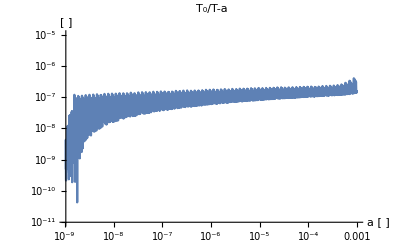

```mathematica
LogLogPlot[1-T/("T0")a /.T->(30/(π^2 3.38)(ρSMt/.ρSM[[1]])[a])^(1/4)/."T0"->10^-9"Td"/.CosmoParams[],{a,10^-9,10^-3},PlotLabel->"T_0/T-a",AxesLabel->{"a [ ]","[ ]"},PlotRange->{10^-11,10^-5}]
```

#### DS Energy Density Boltzmann Approximate Analytic Evolution Unit Testing - Just DS

As in the above sections, we make the assumption that m_e_D=m_e and m_p_D=m_p, we also take f_D=0.01

```mathematica
Print["we need the source term <dE_tr/(dt dV)> the energy transfer rate per unit time and volume from the SM to the DS. The integrand of corresponding integral is simply n_D E_t dΓ/dt"]
nD EttotheldΓdEt/.l->1/.msrepl/.mD->m//Simplify//PowerExpand
Print["We can substitute an expression for nD in terms of it's approximate scaling"]
%%/.nD->nD00/(("T0")^3 β^3)
Print["We now take the leading order expression in E_t. As we have shown above this function is peaked at Λ << T. And m β >> 1 "]
(*(Series[%%/.β->ξβ/m ,{ξβ,∞,7}]//Normal)/.ξβ->β m
Series[%/.Et->ξEt m,{ξEt,0,1}]*)
("g" "n0" ("α")^2 ⅇ^(-Et β) Et nD00 ((2 m)^2 β^2) κ^2)/(2 ("T0")^6 "Z1" ("Λ"+Et)^2 m π β^9)
Integrate[%,Et]
%/.Et->0
Print["The evaluation of the integral at ∞ is 0, and so expanding the integral in a series in Λ β << 1 (drop the log term)"]
(Series[%%/."Λ"->ξΛ β^-1,{ξΛ,0,0}]/.Arg[ξΛ]->0//Normal)/.ξΛ-> "Λ"β
(*ExpandeddEtrdtdV=%/."Λ"->β^-1/.thermalrepl//PowerExpand*)
ExpandeddEtrdtdV=-%/.thermalrepl//PowerExpand
```

we need the source term <dE_tr/(dt dV)> the energy transfer rate per unit time and volume from the SM to the DS. The integrand of corresponding integral is simply n_D E_t dΓ/dt

(g n0 α^2 ⅇ^(-Et β) Et nD (4+2 (Et+2 m) β+(Et+2 m)^2 β^2) κ^2)/(2 T0^3 Z1 (Λ+Et)^2 m π β^6)

We can substitute an expression for nD in terms of it's approximate scaling

(g n0 α^2 ⅇ^(-Et β) Et nD00 (4+2 (Et+2 m) β+(Et+2 m)^2 β^2) κ^2)/(2 T0^6 Z1 (Λ+Et)^2 m π β^9)

We now take the leading order expression in E_t. As we have shown above this function is peaked at Λ << T. And m β >> 1

(2 g n0 α^2 ⅇ^(-Et β) Et m nD00 κ^2)/(T0^6 Z1 (Λ+Et)^2 π β^7)

(2 g n0 α^2 m nD00 κ^2 ((Λ ⅇ^(-Et β))/(Λ+Et)+ⅇ^(Λ β) (1+Λ β) ExpIntegralEi[-((Λ+Et) β)]))/(T0^6 Z1 π β^7)

(2 g n0 α^2 m nD00 κ^2 (1+ⅇ^(Λ β) (1+Λ β) ExpIntegralEi[-Λ β]))/(T0^6 Z1 π β^7)

The evaluation of the integral at ∞ is 0, and so expanding the integral in a series in Λ β << 1 (drop the log term)

(2 g n0 α^2 m nD00 κ^2 (1+EulerGamma+Log[Λ β]))/(T0^6 Z1 π β^7)

-(4 n0 α^2 nD00 √(2 π) κ^2 (1+EulerGamma-2 Log[T0]+Log[Λ0]-Log[β]))/(T0^6 √m β^(11/2))

```mathematica
Print["Now use this expanded expression to solve for the DS energy density"]
ρDsolAna=DSolve[(("T0")/(Hr/β)(ExpandeddEtrdtdV-4 Hr/(β^2"T0") ρDt[β]))==ρDt'[β],ρDt[β],β][[1]]
```

Now use this expanded expression to solve for the DS energy density

{ρDt[β]→C[1]/β^4-(8 n0 α^2 nD00 √(2 π) κ^2 (3+EulerGamma-2 Log[T0]+Log[Λ0]-Log[β]))/(T0^5 Hr √m β^(7/2))}

Now find Hr such that T0/β^2 = H during radiation domination

Hr==5.87598×10^-32

Compare this approximation for H to the true value. The ratio of approximate to real is

0.49418

Substitute this into the ODE solution

{ρDt[β]→C[1]/β^4-(5.54995 κ^2 (-32.8877-Log[β]))/β^(7/2)}

Now solve the initial condition so that the energy density is 0 at decoupling

{C[1]→-0.155134 κ^2}

{ρDt[β]→(κ^2 (-0.155134+182.525 √β+5.54995 √β Log[β]))/β^4}

Now plot the solution for κ = 10^-4.5 as we did above for the numerical solution

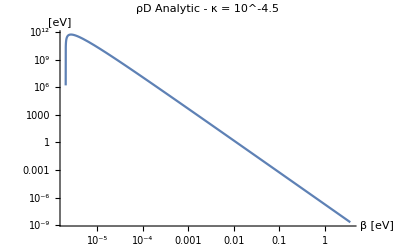

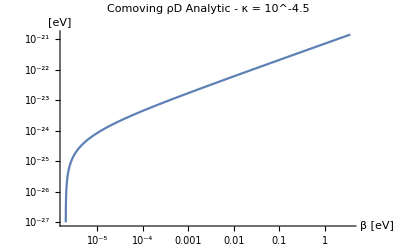

Note that this plot qualitatively matches the numerical solution. The DS temperature at recombination is then

2.06787×10^-9

```mathematica
Print["Now find Hr such that (<T0>)/β^2 = H during radiation domination"]
(*Hrsol =((H[("Td")^-1] 1/("T0")/.CosmoParams[])-(H[10("Td")^-1] 1/("T0")/.CosmoParams[]))/((10("Td")^-1)^2-("Td")^-2/.CosmoParams[])*)
Hrsol=(H[("Td")^-1]("T0")/("Td")^2/.CosmoParams[]);
Hr==Hrsol
Print["Compare this approximation for H to the true value. The ratio of approximate to real is"]
("TR")^2/("T0")Hrsol/.CosmoParams[];
H[1/("TR")]/.CosmoParams[];
%%/%
Print["Substitute this into the ODE solution"]
ρDsolAna/.nD00->nD0[0.01,2000"me"]/.Λrepl/.m->"me"/.CosmoParams[]/.Hr->Hrsol
Print["Now solve the initial condition so that the energy density is 0 at decoupling"]
ρDc1sol=Solve[(ρDt[β]/.%%/.β->1/("Td")/.CosmoParams[])==0,C[1]][[1]]
NρDsolAna=%%%/.ρDc1sol//Simplify
Print["Now plot the solution for κ = 10^-4.5 as we did above for the numerical solution"]
(*LogLogPlot[ρDt[β]/.NρDsolAna/.κ->10^-3.9,{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]}]*)
LogLogPlot[ρDt[β]/.NρDsolAna/.κ->10^-4.5,{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},AxesLabel->{"β [eV]","[eV]"},PlotLabel->"ρD Analytic - κ = 10^-4.5"]
LogLogPlot[β^4("T0")^4 ρDt[β]/.NρDsolAna/.κ->10^-4.5/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},AxesLabel->{"β [eV]","[eV]"},PlotLabel->"Comoving ρD Analytic - κ = 10^-4.5"]
Print["Note that this plot qualitatively matches the numerical solution. The DS temperature at recombination is then"]
TDAnaR=ρDt[β]/.NρDsolAna/.β->1/("TR")/.CosmoParams[]/.κ->10^-4.5
```

```mathematica
(*ρD[β_]:= ("me"+2000 "me")nD0[0.01,10^9]/(("T0")^3 β^3)+ ργD[β]/.CosmoParams[]*)
```

```mathematica
Print["We can solve for the corresponding DS temperature (and check our assumption that the DS is radiation dominated)"]
TDsol=NSolve[3 TD (nDR[0.01,10^9]+π^2/45 TD^3/.CosmoParams[])==TDAnaR,TD][[4]]
Print["The ratio of matter to radiation ρ_m/ρ_r is:"]
(3 TD (nDR[0.01,10^9]))/(3 TD (π^2/45 TD^3))/.CosmoParams[]/.TDsol
Print["So our approximation of a radiation dominated dark sector is entirely valid. \n\nNow compute N_eff given our DS temperature"]
gstar=2 (TD/"TR")^4/.TDsol/.CosmoParams[];(* []effective gstar for dark photon at recombination*)
ΔNeff = 8/7 (11/4)^(4/3) gstar(*[]*)
Print["So comparing the two methods - numerical and analytical - are give nearly identical constraints"]
```

We can solve for the corresponding DS temperature (and check our assumption that the DS is radiation dominated)

{TD→0.00748735}

The ratio of matter to radiation ρ_m/ρ_r is:

1.54283×10^-6

So our approximation of a radiation dominated dark sector is entirely valid. 

Now compute N_eff given our DS temperature

4.83929×10^-6

So comparing the two methods - numerical and analytical - are give nearly identical constraints

#### Numerical Boltzmann Evolution of both sectors

```mathematica
2 + 2 7/8 (4/11)^(4/3)3.046//N
```

3.38354